## Exercises: Evaluation

```mathematica
Clear[f]
```

### Exercise1 Set an attribute for a symbol f so that f[{1,2},{3,4}] evaluates to {f[1,3],f[2,4]} .

```mathematica
SetAttributes[f,Listable]
f[{1,2},{3,4}]
```

{f[1,3],f[2,4]}

### Define a function S[p_] that holds the argument p unevaluated and that returns the list {Hold[p],p}. For example, the definition of S should give: S[2+2] {Hold[2+2],4}

```mathematica
SetAttributes[S,HoldFirst];S[p_] := {Hold[p], p}
S[2+2]
```

{Hold[2+2],4}

### Exercise3

```mathematica
Hold[Echo[2],Echo[1]]/.Hold[p_,q_]:>With[{x=p,y=q},{y,x}]
```

2

1

{1,2}

```mathematica
Hold[Echo[1],Echo[2]]/.Hold[p_,q_]:>With[{y=q,x=p},{x,y}]
```

2

1

{1,2}

## Exercises: Expressions

### Exercise1 Define a function f[x_,y_] that adds x and y and displays the result in full form notation.

```mathematica
f[x_,y_] := FullForm[x+y]
f[e,r]
```

Plus[e,r]

### Exercise2 Define a pure function a[list_] that counts how many elements of a list are atoms and how many are not.

```mathematica
Ca[list_]:=Counts[AtomQ/@list]
Ca[{1,2.3,"allo", f[]}]
```

<|True→3,False→1|>

## Exercises: Notation

### Exercise1 Change the following expression so that this evaluation returns 1,3,5

```mathematica
Sqrt@First/@{{1,2},{3,4},{5,6}}
```

{√First[{1,2}],√First[{3,4}],√First[{5,6}]}

```mathematica
Sqrt@(First/@{{1,2},{3,4},{5,6}})
```

{1,√3,√5}

### Exercise2 Open the documentation pages of the functions used in the following expression:

```mathematica
(7^2)[[0]]
```

```mathematica
FullForm[Hold[(7^2)[[0]]]]
```

Hold[Part[Power[7,2],0]]

### Exercise3 Use FullForm and StringReplace to write a function names[list_] that returns the names of special characters, as shown below:

```mathematica
names[list_]:=StringReplace[ToString@FullForm[#],{"\\["->"","]"->""}]&/@list
names@{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}
```

{Alpha,Beta,Gamma,Delta,CurlyEpsilon,Zeta,Eta,Theta,Iota,Kappa,Lambda,Mu,Nu,Xi,Omicron,Pi,Rho,Sigma,Tau,Upsilon,CurlyPhi,Chi,Psi,Omega}

## Exercises: Assignments and Evaluation Rules

### Exercise1 Use assignments to introduce evaluation rules that have the same effect as the rules in this input:

```mathematica
ClearAll[g]
g[5]//.{g[0]->0,g[p_]:>p+g[p-1]}
```

15

```mathematica
g[0]=0
g[p_]:=p+g[p-1]
g[5]
```

0

15

### Exercise2 Use a tagged assignment to set up an evaluation rule to replace any integer power of any expression of the form x[_] with zero.

```mathematica
ClearAll[x]
x/:x[_]^_Integer=0
```

### Exercise3 Use assignments in a Do loop to create evaluation rules to replace g[n][p_] with f[np] for n from 1 to 10.

```mathematica
ClearAll[g]
Do[g[n][p_] = f[n p],{n,10}]
```

## Exercises: Local Variables

### Exercise1 Use Module to modify this definition of f[p_] to localize all of the variables that are not already local to the definition:

```mathematica
f[p_Integer?Positive]:=(k=π/2;Table[Sin[n k],{n,0,p}])
f[p_Integer?Positive]:=Module[{k},k=π/2;Table[Sin[n k],{n,0,p}]] 
Clear[f]
```

### Exercise2 Change the input in this example to localize x so that the result is the same list of pure functions even if x has a global value:

```mathematica
Table[Function[x,Evaluate[k x]],{k,3}]
```

{Function[x,x],Function[x,2 x],Function[x,3 x]}

```mathematica
x=5;Block[{x},Table[Function[x,Evaluate[k x]],{k,3}]]
```

{Function[x,x],Function[x,2 x],Function[x,3 x]}

```mathematica
Clear[x]
```

### Exercise3 Rewrite this input to do an equivalent calculation using Function rather than With:

```mathematica
With[{x=99},Total[Last/@FactorInteger[x]]]
```

Function[x,Total[Last/@FactorInteger[x]]]

```mathematica
Function[x,Total[Last/@FactorInteger[x]]][99]
```

3

## Exercises: Patterns

### Exercise1 Change this input to use a Condition pattern rather than Except[1|5] to pick out elements other than 1 and 5 from the list:

```mathematica
Cases[{1,2,4,3,5,1,3,1,4},Except[1|5]]
```

{2,4,3,3,4}

```mathematica
Cases[{1,2,4,3,5,1,3,1,4},b_/;2<= b<=4 ]
```

{2,4,3,3,4}

### Exercise2 Apply a rule to this list to replace the longest sequence of ones in the list with the string “ones”

```mathematica
{1,3,1,1,3,1,1,1,3,1,3}
```

```mathematica
{1,3,1,1,3,1,1,1,3,1,3}/.{p___, Longest[q:1..], r___} :>{p,"ones",r}
```

{1,3,1,1,3,ones,3,1,3}

## Exercises: Flat and Orderless Operations

### Exercise1 Change the attributes of f so that this evaluation returns f[1,2,3,4,5]:

```mathematica
f[f[2,3,4],f[5,1]]
Attributes[f]
```

f[f[2,3,4],f[5,1]]

{}

```mathematica
SetAttributes[f,{Orderless, Flat}]
f[f[2,3,4],f[5,1]]
```

f[1,2,3,4,5]

### Exercise2 Change the attributes of f so that this evaluation returns {G[1],G[3]}:

```mathematica
SetAttributes[f,OneIdentity]
{f[1,2],f[2,3]}/.f[2,p_]->G[p]
```

{G[1],G[3]}

### Exercise3 Change the attributes of f so that the result is f[3,{f[1,2]}]:

```mathematica
f[1,2,3,1,2]/.f[p_,p_]->{p}
```

f[3,{f[1,2]}]

```mathematica
ClearAll[f]
```

## Exercises: Sequence and Nothing

### Exercise1 Use Unevaluated to fix this program so that the warning message is not generated and the sequence of options inserted into the Plot expression is evaluated:

Plot::nonopt: Options expected (instead of opts) beyond position 2 in Plot[Sin[π x],{x,0,3},opts]. An option must be a rule or a list of rules.

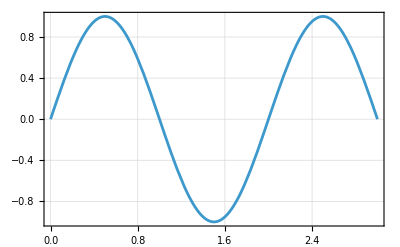

```mathematica
Plot[Sin[π x],{x,0,3},opts]/.opts->Sequence[Frame->True,GridLines->Automatic]
```

```mathematica
Unevaluated[Plot[Sin[π x],{x,0,3},opts]]/.opts->Sequence[Frame->True,GridLines->Automatic]
```

-Graphics-

### Exercise2 Use replacement by Nothing to remove the points from the Graphics expression that is created by this input:

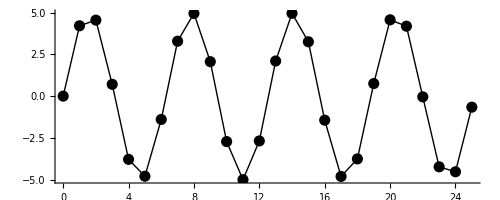

```mathematica
With[{pts=Table[{k,5Sin[k]},{k,0,25}]},Graphics[{Line[pts],PointSize[0.02],Point/@pts},Axes->True]]
```

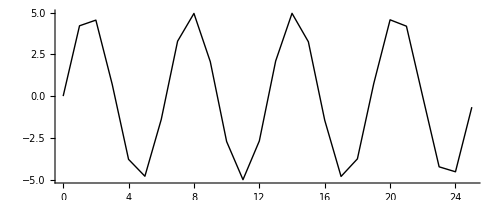

```mathematica
With[{pts=Table[{k,5Sin[k]},{k,0,25}]},Graphics[{Line[pts],PointSize[0.02],Point/@pts},Axes->True]]/. _Point -> Nothing
```

### Exercise3 Fix this program to step through the list using a Do loop, but to delete the ones as intended instead of failing after generating messages:

```mathematica
x={0,1,2,0,1,2,0,1,2};
Do[If[x[[k]]==1,x[[k]]=Nothing],{k,Length[x]}]
x
```

Part::partw: Part 7 of {0,2,1,0,1,2} does not exist.

Part::partw: Part 8 of {0,2,1,0,1,2} does not exist.

Part::partw: Part 9 of {0,2,1,0,1,2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0,2,1,0,1,2}

```mathematica
x={0,1,2,0,1,2,0,1,2};
Do[
If[x[[k]]==1,x[[k]]=Nothing],{k,Length[x],1,-1}]
x
```

{0,2,0,2,0,2}

```mathematica
ClearAll[x]
```